## Функция правдоподобия

Вычислим функцию правдоподобия для пары картинок -- одна с изображением звезды и другая с изображением галактики. Обозначим θ - набор параметров от которых зависит изображение, n_s[x,y] - число зарегистрированных фотонов в точке (x,y) на картинке со звездой, n_g[x,y] - то же замое для картинки с галактикой. Считая наблюдения в отдельных точках независимыми, получаем:

P[n_s,n_g;θ]=∏_(x=1)^Nx ∏_(y=1)^Ny P_s[n_s[x,y];θ]P_g[n_g[x,y];θ]
Log[P[n_s,n_g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (Log[P_s[n_s[x,y];θ]]+Log[P_g[n_g[x,y];θ]])

### Пуассоновское распределение

#### Вид функции правдоподобия

Пусть n_(s,g)[x,y] имеет Пуассоновское распределение с параметром λ_(s,g)[x,y], где λ_(s,g)[x,y] - интенсивность потока фотонов в точке (x,y) (фактически - матожидание числа фотонов пришедших в точку (x,y) за время экспозиции). Тогда

Log[P[n_s,n_g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny Log[(λ_s[x,y;θ]^n_s[x,y]Exp[-λ_s[x,y;θ]])/(n_s[x,y]!)]Log[(λ_g[x,y;θ]^n_g[x,y]Exp[-λ_g[x,y;θ]])/(n_g[x,y]!)]=∑_(x=1)^Nx ∑_(y=1)^Ny (Log[λ_s[x,y;θ]]n_s[x,y]-λ_s[x,y;θ]-Log[n_s[x,y]!]+Log[λ_g[x,y;θ]]n_g[x,y]-λ_g[x,y;θ]-Log[n_g[x,y]!])

Однако нам известны не число попавших фотонов, а отсчёт прибора (значение яркости пиксела) s[x,y]. Будем считать что для изменения яркости пиксела на 1 уровень нужно k фотонов, т.е. n[x,y]=k s[x,y], причём k≥1 (при k<1 прибор может среагировать даже если фотон на него не попал, что было бы странно). Тогда функция распределения для единичного пиксела равна:

P[s[x,y];θ]=k(λ[x,y;θ]^(k s[x,y])Exp[-λ[x,y;θ]])/((k s[x,y])!)

Обратите внимание на множитель k который появился в выражении для вероятности -- он нужен для сохранения нормировки. Функция правдоподобия для всей картинки:

Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny Log[P_s[s[x,y];θ]P_g[g[x,y];θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (Log[k_s(λ_s[x,y;θ]^(k_s s[x,y])Exp[-λ_s[x,y;θ]])/((k_s s[x,y])!)k_g(λ_g[x,y;θ]^(k_g g[x,y])Exp[-λ_g[x,y;θ]])/((k_g g[x,y])!)])=Nx Ny Log[k_s k_g]+∑_(x=1)^Nx ∑_(y=1)^Ny (k_s Log[λ_s[x,y;θ]]s[x,y]-λ_s[x,y;θ]-Log[k_s s[x,y]!]+k_g Log[λ_g[x,y;θ]]g[x,y]-λ_g[x,y;θ]-Log[k_g g[x,y]!])

По-идее, k принимает только целые значения. Но мы разрешим ему принимать действительные значения и перейдём от факториала к непрерывной гамма-функции, чтобы использовать градиентные методы поиска экстремума:

Log[P[s,g;θ]]=Nx Ny Log[k_s k_g]+∑_(x=1)^Nx ∑_(y=1)^Ny (k_s Log[λ_s[x,y;θ]]s[x,y]-λ_s[x,y;θ]-LogGamma[k_s s[x,y]+1]+k_g Log[λ_g[x,y;θ]]g[x,y]-λ_g[x,y;θ]-LogGamma[k_g g[x,y]+1])

#### Производные функции правдоподобия

```mathematica
D[Nx Ny Log[Subscript[k, s] Subscript[k, g]]+∑_(x=1)^Nx ∑_(y=1)^Ny (Subscript[k, s] Log[Subscript[λ, s][x,y,θ]]s[x,y]-Subscript[λ, s][x,y,θ]-LogGamma[Subscript[k, s] s[x,y]+1]+Subscript[k, g] Log[Subscript[λ, g][x,y,θ]]g[x,y]-Subscript[λ, g][x,y,θ]-LogGamma[Subscript[k, g] g[x,y]+1]),{{θ,Subscript[k, s],Subscript[k, g]}}]
```

{∑_(x=1)^Nx ∑_(y=1)^Ny (-(λ_g)^(0,0,1)[x,y,θ]+(g[x,y] k_g (λ_g)^(0,0,1)[x,y,θ])/λ_g[x,y,θ]-(λ_s)^(0,0,1)[x,y,θ]+(s[x,y] k_s (λ_s)^(0,0,1)[x,y,θ])/λ_s[x,y,θ]),(Nx Ny)/k_s+∑_(x=1)^Nx ∑_(y=1)^Ny (Log[λ_s[x,y,θ]] s[x,y]-PolyGamma[0,1+s[x,y] k_s] s[x,y]),(Nx Ny)/k_g+∑_(x=1)^Nx ∑_(y=1)^Ny (g[x,y] Log[λ_g[x,y,θ]]-g[x,y] PolyGamma[0,1+g[x,y] k_g])}

Получаем:

∂_θ Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (((k_s s[x,y])/λ_s[x,y,θ]-1)(λ_s)^(0,0,1)[x,y,θ]+((k_g g[x,y])/λ_g[x,y,θ]-1)(λ_g)^(0,0,1)[x,y,θ]),
∂_k_s Log[P[s,g;θ]]=(Nx Ny)/k_s+∑_(x=1)^Nx ∑_(y=1)^Ny s[x,y](Log[λ_s[x,y,θ]] -PolyGamma[0,1+k_s s[x,y]]),
∂_k_g Log[P[s,g;θ]]=(Nx Ny)/k_g+∑_(x=1)^Nx ∑_(y=1)^Ny g[x,y](Log[λ_g[x,y,θ]] -PolyGamma[0,1+k_g g[x,y]])

### Гауссовское распределение

#### Вид функции правдоподобия

Пусть n_(s,g)[x,y] имеет Гауссово распределение с матожиданием μ_(s,g)[x,y] и дисперсией σ_(s,g), где μ_(s,g)[x,y] - интенсивность потока фотонов в точке (x,y) (фактически - матожидание числа фотонов пришедших в точку (x,y) за время экспозиции). Тогда

```mathematica
∑_(x=1)^Nx ∑_(y=1)^Ny Log[PDF[NormalDistribution[Subscript[μ, s][x,y,θ],Subscript[σ, s]],Subscript[n, s][x,y]]]
%/.Log[x_Times]:>Map[Log,Apply[Plus,x]]
L=%/.Log[a_^b_]->b Log[a]
```

∑_(x=1)^Nx ∑_(y=1)^Ny Log[(ⅇ^(-(n_s[x,y]-μ_s[x,y,θ])^2/(2 σ_s^2)))/(√(2 π) σ_s)]

∑_(x=1)^Nx ∑_(y=1)^Ny (Log[ⅇ^(-(n_s[x,y]-μ_s[x,y,θ])^2/(2 σ_s^2))]-1/2 Log[2 π]+Log[1/σ_s])

∑_(x=1)^Nx ∑_(y=1)^Ny (-1/2 Log[2 π]-Log[σ_s]-(n_s[x,y]-μ_s[x,y,θ])^2/(2 σ_s^2))

Имеем

Log[P[n_s,n_g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (-1/2 Log[2 π]-Log[σ_s]-(-Is h_s[x,y,θ]+n_s[x,y])^2/(2 σ_s^2))=(-1/2 Log[2 π]-Log[σ_s])Nx Ny-1/(2 σ_s^2)∑_(x=1)^Nx ∑_(y=1)^Ny (n_s[x,y]-Is h_s[x,y,θ])^2

Найдём оптимальное значение для σ_s:

```mathematica
L=(-1/2 Log[2 π]-Log[Subscript[σ, s]])Nx Ny-1/(2 Subscript[σ, s]^2)∑_(x=1)^Nx ∑_(y=1)^Ny (Subscript[n, s][x,y]-Subscript[μ, s][x,y,θ])^2
Solve[D[L,Subscript[σ, s]]==0,Subscript[σ, s]]//FullSimplify
```

Nx Ny (-1/2 Log[2 π]-Log[σ_s])-(∑_(x=1)^Nx ∑_(y=1)^Ny (n_s[x,y]-μ_s[x,y,θ])^2)/(2 σ_s^2)

{{σ_s→-(√(∑_(x=1)^Nx ∑_(y=1)^Ny (n_s[x,y]-μ_s[x,y,θ])^2))/(√Nx √Ny)},{σ_s→(√(∑_(x=1)^Nx ∑_(y=1)^Ny (n_s[x,y]-μ_s[x,y,θ])^2))/(√Nx √Ny)}}

Оптимальное значение для Is:

```mathematica
L/.Subscript[μ, s][x__]->Is Subscript[h, s][x]
D[%,Is]
```

Nx Ny (-1/2 Log[2 π]-Log[σ_s])-(∑_(x=1)^Nx ∑_(y=1)^Ny (-Is h_s[x,y,θ]+n_s[x,y])^2)/(2 σ_s^2)

-(∑_(x=1)^Nx ∑_(y=1)^Ny -2 h_s[x,y,θ] (-Is h_s[x,y,θ]+n_s[x,y]))/(2 σ_s^2)

-(∑_(x=1)^Nx ∑_(y=1)^Ny -2 h_s[x,y,θ] (-Is h_s[x,y,θ]+n_s[x,y]))/(2 σ_s^2)=1/σ_s^2(-Is∑_(x=1)^Nx ∑_(y=1)^Ny h_s[x,y,θ]^2+∑_(x=1)^Nx ∑_(y=1)^Ny h_s[x,y,θ] n_s[x,y])

```mathematica
Solve[-Is∑_(x=1)^Nx ∑_(y=1)^Ny (Subscript[h, s][x,y,θ])^2+∑_(x=1)^Nx ∑_(y=1)^Ny Subscript[h, s][x,y,θ] Subscript[n, s][x,y]==0,Is]
```

{{Is→(∑_(x=1)^Nx ∑_(y=1)^Ny h_s[x,y,θ] n_s[x,y])/(∑_(x=1)^Nx ∑_(y=1)^Ny h_s[x,y,θ]^2)}}

Что в общем-то и ожидалось.

#### Производные функции правдоподобия

```mathematica
D[L,{{θ,Subscript[μ, s][x,y,θ]}}]
```

{0,-(∑_(x=1)^Nx ∑_(y=1)^Ny -2 (n_s[x,y]-μ_s[x,y,θ]))/(2 σ_s^2)}

Получаем:

∂_θ Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (((k_s s[x,y])/λ_s[x,y,θ]-1)(λ_s)^(0,0,1)[x,y,θ]+((k_g g[x,y])/λ_g[x,y,θ]-1)(λ_g)^(0,0,1)[x,y,θ]),
∂_k_s Log[P[s,g;θ]]=(Nx Ny)/k_s+∑_(x=1)^Nx ∑_(y=1)^Ny s[x,y](Log[λ_s[x,y,θ]] -PolyGamma[0,1+k_s s[x,y]]),
∂_k_g Log[P[s,g;θ]]=(Nx Ny)/k_g+∑_(x=1)^Nx ∑_(y=1)^Ny g[x,y](Log[λ_g[x,y,θ]] -PolyGamma[0,1+k_g g[x,y]])

#### Вторые производные функции правдоподобия

```mathematica
D[Nx Ny Log[Subscript[k, s] Subscript[k, g]]+∑_(x=1)^Nx ∑_(y=1)^Ny (Subscript[k, s] Log[Subscript[λ, s][x,y,θ]]s[x,y]-Subscript[λ, s][x,y,θ]-LogGamma[Subscript[k, s] s[x,y]+1]+Subscript[k, g] Log[Subscript[λ, g][x,y,θ]]g[x,y]-Subscript[λ, g][x,y,θ]-LogGamma[Subscript[k, g] g[x,y]+1]),{{θ,Subscript[k, s],Subscript[k, g]},2}]//FullSimplify//TableForm
```

∑_(x=1)^Nx ∑_(y=1)^Ny (-(g[x,y] k_g ((λ_g)^(0,0,1)[x,y,θ])^2)/λ_g[x,y,θ]^2-(s[x,y] k_s ((λ_s)^(0,0,1)[x,y,θ])^2)/λ_s[x,y,θ]^2-(λ_g)^(0,0,2)[x,y,θ]+(g[x,y] k_g (λ_g)^(0,0,2)[x,y,θ])/λ_g[x,y,θ]-(λ_s)^(0,0,2)[x,y,θ]+(s[x,y] k_s (λ_s)^(0,0,2)[x,y,θ])/λ_s[x,y,θ]) | ∑_(x=1)^Nx ∑_(y=1)^Ny (s[x,y] (λ_s)^(0,0,1)[x,y,θ])/λ_s[x,y,θ] | ∑_(x=1)^Nx ∑_(y=1)^Ny (g[x,y] (λ_g)^(0,0,1)[x,y,θ])/λ_g[x,y,θ]
∑_(x=1)^Nx ∑_(y=1)^Ny (s[x,y] (λ_s)^(0,0,1)[x,y,θ])/λ_s[x,y,θ] | -(Nx Ny)/k_s^2+∑_(x=1)^Nx ∑_(y=1)^Ny -PolyGamma[1,1+s[x,y] k_s] s[x,y]^2 | 0
∑_(x=1)^Nx ∑_(y=1)^Ny (g[x,y] (λ_g)^(0,0,1)[x,y,θ])/λ_g[x,y,θ] | 0 | -(Nx Ny)/k_g^2+∑_(x=1)^Nx ∑_(y=1)^Ny -g[x,y]^2 PolyGamma[1,1+g[x,y] k_g]

Получаем :

∂_θ ∂_θ Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (-(k_s s[x,y] ((λ_s)^(0,0,1)[x,y,θ])^2)/λ_s[x,y,θ]^2+((k_s s[x,y])/λ_s[x,y,θ]-1)(λ_s)^(0,0,2)[x,y,θ]-(k_g g[x,y] ((λ_g)^(0,0,1)[x,y,θ])^2)/λ_g[x,y,θ]^2+((k_g g[x,y])/λ_g[x,y,θ]-1)(λ_g)^(0,0,2)[x,y,θ])
∂_k_s ∂_θ Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (s[x,y] (λ_s)^(0,0,1)[x,y,θ])/λ_s[x,y,θ]
∂_k_g ∂_θ Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (g[x,y] (λ_g)^(0,0,1)[x,y,θ])/λ_g[x,y,θ]
∂_k_s ∂_k_s Log[P[s;θ]]=-(Nx Ny)/k_s^2-∑_(x=1)^Nx ∑_(y=1)^Ny PolyGamma[1,1+k_s s[x,y]] s[x,y]^2
∂_k_g ∂_k_s Log[P[s;θ]]=0
∂_k_g ∂_k_g Log[P[s;θ]]=-(Nx Ny)/k_g^2-∑_(x=1)^Nx ∑_(y=1)^Ny PolyGamma[1,1+k_g g[x,y]] g[x,y]^2

### Пуассоновское распределение, λ≫1

#### Вид функции правдоподобия

Пусть n_(s,g)[x,y] имеет Пуассоновское распределение с матожиданием λ_(s,g)[x,y], причём λ_(s,g)[x,y]≫1. Тогда распределение близко к Гауссовскому с матожиданием равным дисперсии и равным μ_(s,g)[x,y]. Тогда

```mathematica
∑_(x=1)^Nx ∑_(y=1)^Ny (Log[PDF[NormalDistribution[Subscript[μ, s][x,y,θ],Subscript[μ, s][x,y,θ]],Subscript[n, s][x,y]]]+Log[PDF[NormalDistribution[Subscript[μ, g][x,y,θ],Subscript[μ, g][x,y,θ]],Subscript[n, g][x,y]]])
FunctionExpand[%,{Subscript[μ, s][x,y,θ]>0,Subscript[μ, g][x,y,θ]>0}]
%/.{Log[Exp[x_]]->x,Log[1/x_]->-Log[x]}/.-(a_-b_)^2/(2 b_^2)->-1/2(a/b-1)^2
```

∑_(x=1)^Nx ∑_(y=1)^Ny (Log[(ⅇ^(-(n_g[x,y]-μ_g[x,y,θ])^2/(2 μ_g[x,y,θ]^2)))/(√(2 π) μ_g[x,y,θ])]+Log[(ⅇ^(-(n_s[x,y]-μ_s[x,y,θ])^2/(2 μ_s[x,y,θ]^2)))/(√(2 π) μ_s[x,y,θ])])

∑_(x=1)^Nx ∑_(y=1)^Ny (Log[ⅇ^(-(n_g[x,y]-μ_g[x,y,θ])^2/(2 μ_g[x,y,θ]^2))]+Log[ⅇ^(-(n_s[x,y]-μ_s[x,y,θ])^2/(2 μ_s[x,y,θ]^2))]-Log[2 π]+Log[1/μ_g[x,y,θ]]+Log[1/μ_s[x,y,θ]])

∑_(x=1)^Nx ∑_(y=1)^Ny (-Log[2 π]-Log[μ_g[x,y,θ]]-Log[μ_s[x,y,θ]]-1/2 (-1+n_g[x,y]/μ_g[x,y,θ])^2-1/2 (-1+n_s[x,y]/μ_s[x,y,θ])^2)

Имеем

Log[P[n_s,n_g;θ]]=-Nx Ny Log[2 π ]-∑_(x=1)^Nx ∑_(y=1)^Ny (Log[μ_g[x,y,θ]]+Log[μ_s[x,y,θ]]+1/2 (-1+n_g[x,y]/μ_g[x,y,θ])^2+1/2 (-1+n_s[x,y]/μ_s[x,y,θ])^2)

#### Производные функции правдоподобия

```mathematica
D[-Nx Ny Log[2 π ]-∑_(x=1)^Nx ∑_(y=1)^Ny (Log[Subscript[μ, g][x,y,θ]]+Log[Subscript[μ, s][x,y,θ]]+1/2 (-1+(Subscript[n, g][x,y])/(Subscript[μ, g][x,y,θ]))^2+1/2 (-1+(Subscript[n, s][x,y])/(Subscript[μ, s][x,y,θ]))^2),θ]
```

-∑_(x=1)^Nx ∑_(y=1)^Ny (-(n_g[x,y] (-1+n_g[x,y]/μ_g[x,y,θ]) (μ_g)^(0,0,1)[x,y,θ])/μ_g[x,y,θ]^2+((μ_g)^(0,0,1)[x,y,θ])/μ_g[x,y,θ]-(n_s[x,y] (-1+n_s[x,y]/μ_s[x,y,θ]) (μ_s)^(0,0,1)[x,y,θ])/μ_s[x,y,θ]^2+((μ_s)^(0,0,1)[x,y,θ])/μ_s[x,y,θ])

Получаем:

∂_θ Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny ((n_g[x,y] (-1+n_g[x,y]/μ_g[x,y,θ]) (μ_g)^(0,0,1)[x,y,θ])/μ_g[x,y,θ]^2-((μ_g)^(0,0,1)[x,y,θ])/μ_g[x,y,θ]+(n_s[x,y] (-1+n_s[x,y]/μ_s[x,y,θ]) (μ_s)^(0,0,1)[x,y,θ])/μ_s[x,y,θ]^2-((μ_s)^(0,0,1)[x,y,θ])/μ_s[x,y,θ])=∑_(x=1)^Nx ∑_(y=1)^Ny (((n_g[x,y] (-1+n_g[x,y]/μ_g[x,y,θ]))/μ_g[x,y,θ]^2-1/μ_g[x,y,θ])(μ_g)^(0,0,1)[x,y,θ]+((n_s[x,y] (-1+n_s[x,y]/μ_s[x,y,θ]))/μ_s[x,y,θ]^2-1/μ_s[x,y,θ])(μ_s)^(0,0,1)[x,y,θ])

#### Вторые производные функции правдоподобия

```mathematica
D[Nx Ny Log[Subscript[k, s] Subscript[k, g]]+∑_(x=1)^Nx ∑_(y=1)^Ny (Subscript[k, s] Log[Subscript[λ, s][x,y,θ]]s[x,y]-Subscript[λ, s][x,y,θ]-LogGamma[Subscript[k, s] s[x,y]+1]+Subscript[k, g] Log[Subscript[λ, g][x,y,θ]]g[x,y]-Subscript[λ, g][x,y,θ]-LogGamma[Subscript[k, g] g[x,y]+1]),{{θ,Subscript[k, s],Subscript[k, g]},2}]//FullSimplify//TableForm
```

∑_(x=1)^Nx ∑_(y=1)^Ny (-(g[x,y] k_g ((λ_g)^(0,0,1)[x,y,θ])^2)/λ_g[x,y,θ]^2-(s[x,y] k_s ((λ_s)^(0,0,1)[x,y,θ])^2)/λ_s[x,y,θ]^2-(λ_g)^(0,0,2)[x,y,θ]+(g[x,y] k_g (λ_g)^(0,0,2)[x,y,θ])/λ_g[x,y,θ]-(λ_s)^(0,0,2)[x,y,θ]+(s[x,y] k_s (λ_s)^(0,0,2)[x,y,θ])/λ_s[x,y,θ]) | ∑_(x=1)^Nx ∑_(y=1)^Ny (s[x,y] (λ_s)^(0,0,1)[x,y,θ])/λ_s[x,y,θ] | ∑_(x=1)^Nx ∑_(y=1)^Ny (g[x,y] (λ_g)^(0,0,1)[x,y,θ])/λ_g[x,y,θ]
∑_(x=1)^Nx ∑_(y=1)^Ny (s[x,y] (λ_s)^(0,0,1)[x,y,θ])/λ_s[x,y,θ] | -(Nx Ny)/k_s^2+∑_(x=1)^Nx ∑_(y=1)^Ny -PolyGamma[1,1+s[x,y] k_s] s[x,y]^2 | 0
∑_(x=1)^Nx ∑_(y=1)^Ny (g[x,y] (λ_g)^(0,0,1)[x,y,θ])/λ_g[x,y,θ] | 0 | -(Nx Ny)/k_g^2+∑_(x=1)^Nx ∑_(y=1)^Ny -g[x,y]^2 PolyGamma[1,1+g[x,y] k_g]

Получаем :

∂_θ ∂_θ Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (-(k_s s[x,y] ((λ_s)^(0,0,1)[x,y,θ])^2)/λ_s[x,y,θ]^2+((k_s s[x,y])/λ_s[x,y,θ]-1)(λ_s)^(0,0,2)[x,y,θ]-(k_g g[x,y] ((λ_g)^(0,0,1)[x,y,θ])^2)/λ_g[x,y,θ]^2+((k_g g[x,y])/λ_g[x,y,θ]-1)(λ_g)^(0,0,2)[x,y,θ])
∂_k_s ∂_θ Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (s[x,y] (λ_s)^(0,0,1)[x,y,θ])/λ_s[x,y,θ]
∂_k_g ∂_θ Log[P[s,g;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny (g[x,y] (λ_g)^(0,0,1)[x,y,θ])/λ_g[x,y,θ]
∂_k_s ∂_k_s Log[P[s;θ]]=-(Nx Ny)/k_s^2-∑_(x=1)^Nx ∑_(y=1)^Ny PolyGamma[1,1+k_s s[x,y]] s[x,y]^2
∂_k_g ∂_k_s Log[P[s;θ]]=0
∂_k_g ∂_k_g Log[P[s;θ]]=-(Nx Ny)/k_g^2-∑_(x=1)^Nx ∑_(y=1)^Ny PolyGamma[1,1+k_g g[x,y]] g[x,y]^2

### χ^2-распределение

```mathematica
a^2/.a->{1,2}
```

{1,4}

```mathematica
Refine[1/ρ PDF[ChiSquareDistribution[k],x/ρ],x/ρ>0]
Refine[{Integrate[ %,{x,0,∞}],Integrate[x %,{x,0,∞}]},{ρ>0,k≥1}]
```

(2^(-k/2) ⅇ^(-x/(2 ρ)) (x/ρ)^(-1+k/2))/(ρ Gamma[k/2])

{1,k ρ}

#### Вид функции правдоподобия

Пусть n_(s,g)[x,y] имеет χ^2-распределение с 2-мя степенями свободы и матожиданием 2ρ. Тогда

```mathematica
∑_(x=1)^Nx ∑_(y=1)^Ny Log[Refine[1/ρ PDF[ChiSquareDistribution[k[x,y]],(s[x,y]-Subscript[m, s][x,y,θ])/ρ],(s[x,y]-Subscript[m, s][x,y,θ])/ρ>0]]
%/.Log[x_Times]:>Map[Log,Apply[Plus,x]]
%/.Log[a_^b_]->b Log[a]
%/.Log[x_Times]:>Map[Log,Apply[Plus,x]]
%/.Log[a_^b_]->b Log[a]
L=%/.Sum[x_,a__]:>Sum[FullSimplify[x],a]
```

∑_(x=1)^Nx ∑_(y=1)^Ny Log[(2^(-1/2 k[x,y]) ⅇ^(-(s[x,y]-m_s[x,y,θ])/(2 ρ)) ((s[x,y]-m_s[x,y,θ])/ρ)^(-1+1/2 k[x,y]))/(ρ Gamma[1/2 k[x,y]])]

∑_(x=1)^Nx ∑_(y=1)^Ny (Log[2^(-1/2 k[x,y])]+Log[ⅇ^(-(s[x,y]-m_s[x,y,θ])/(2 ρ))]+Log[1/ρ]+Log[1/Gamma[1/2 k[x,y]]]+Log[((s[x,y]-m_s[x,y,θ])/ρ)^(-1+1/2 k[x,y])])

∑_(x=1)^Nx ∑_(y=1)^Ny (-1/2 k[x,y] Log[2]-Log[ρ]-Log[Gamma[1/2 k[x,y]]]+(-1+1/2 k[x,y]) Log[(s[x,y]-m_s[x,y,θ])/ρ]-(s[x,y]-m_s[x,y,θ])/(2 ρ))

∑_(x=1)^Nx ∑_(y=1)^Ny (-1/2 k[x,y] Log[2]-Log[ρ]-Log[Gamma[1/2 k[x,y]]]+(-1+1/2 k[x,y]) (Log[1/ρ]+Log[s[x,y]]+Log[-m_s[x,y,θ]])-(s[x,y]-m_s[x,y,θ])/(2 ρ))

∑_(x=1)^Nx ∑_(y=1)^Ny (-1/2 k[x,y] Log[2]-Log[ρ]-Log[Gamma[1/2 k[x,y]]]+(-1+1/2 k[x,y]) (-Log[ρ]+Log[s[x,y]]+Log[-m_s[x,y,θ]])-(s[x,y]-m_s[x,y,θ])/(2 ρ))

∑_(x=1)^Nx ∑_(y=1)^Ny 1/2 (-k[x,y] Log[2]-2 Log[ρ]-2 Log[Gamma[1/2 k[x,y]]]+(-2+k[x,y]) (-Log[ρ]+Log[s[x,y]]+Log[-m_s[x,y,θ]])+(-s[x,y]+m_s[x,y,θ])/ρ)

Имеем

Log[P[s;θ]]=∑_(x=1)^Nx ∑_(y=1)^Ny 1/2 (-k[x,y] Log[2]-2 Log[ρ]-2 Log[Gamma[1/2 k[x,y]]]+(-2+k[x,y]) (-Log[ρ]+Log[s[x,y]]+Log[-m_s[x,y,θ]])+(-s[x,y]+m_s[x,y,θ])/ρ)

при условии что

∀_A s[x,y]>m_s[x,y,θ].

Найдём оптимальное значение для ρ:

```mathematica
D[L,ρ]
%/.Sum[x_,a__]:>Sum[FullSimplify[x],a]
```

∑_(x=1)^Nx ∑_(y=1)^Ny 1/2 (-2/ρ-(-2+k[x,y])/ρ-(-s[x,y]+m_s[x,y,θ])/ρ^2)

∑_(x=1)^Nx ∑_(y=1)^Ny -(ρ k[x,y]-s[x,y]+m_s[x,y,θ])/(2 ρ^2)

```mathematica
-1/(2 ρ^2)(ρ ∑_(x=1)^Nx ∑_(y=1)^Ny k[x,y]+∑_(x=1)^Nx ∑_(y=1)^Ny (-s[x,y]+Subscript[m, s][x,y,θ]))
Solve[%==0,ρ]
```

-(ρ ∑_(x=1)^Nx ∑_(y=1)^Ny k[x,y]+∑_(x=1)^Nx ∑_(y=1)^Ny (-s[x,y]+m_s[x,y,θ]))/(2 ρ^2)

{{ρ→-(∑_(x=1)^Nx ∑_(y=1)^Ny (-s[x,y]+m_s[x,y,θ]))/(∑_(x=1)^Nx ∑_(y=1)^Ny k[x,y])}}

#### Производные функции правдоподобия

Производная по m_s[x,y,θ]:

```mathematica
L
D[L,Subscript[m, s][x,y,θ]]
%/.Sum[x_,a__]:>Sum[FullSimplify[x],a]
```

∑_(x=1)^Nx ∑_(y=1)^Ny 1/(2 ρ)(-ρ k[x,y] Log[2 ρ]-2 ρ Log[Gamma[1/2 k[x,y]]]+ρ (-2+k[x,y]) Log[s[x,y]-m_s[x,y,θ]]-s[x,y]+m_s[x,y,θ])

∑_(x=1)^Nx ∑_(y=1)^Ny (1-(ρ (-2+k[x,y]))/(s[x,y]-m_s[x,y,θ]))/(2 ρ)

∑_(x=1)^Nx ∑_(y=1)^Ny 1/2 (1/ρ+(-2+k[x,y])/(-s[x,y]+m_s[x,y,θ]))

### Модель для PSF

Будем считать что:

Функция рассеяния h[x, y, θ] имеет Гауссовский вид

Интенсивность звезды -- суммарное число фотонов от звезды попавших в телескоп за время экспозиции -- равна Is

Присутствует равномерная фоновая засветка λ_0

Тогда:

h[x,y,θ]=1/(2π √Det[Σ])Exp[-1/2{x,y}.Inverse[Σ].{x,y}]
λ[x,y,θ]=λ_s0+Is h[x-x_s0,y-y_s0,θ]=λ0+Is/(2π √Det[Σ])Exp[-1/2{x-x_s0,y-y_s0}.Inverse[Σ].{x-x_s0,y-y_s0}]

Пусть Inverse[Σ]=A. Тогда:

```mathematica
Subscript[λ, s][x,y,θ]=Subscript[λ0, s]+Is h[x-Subscript[x0, s],y-Subscript[y0, s],θ]
Subscript[λ, s][x,y,θ]/.h[x_,y_,θ]->(√Det[A])/(2π)Exp[-1/2{x,y}.A.{x,y}]
```

Is h[x-x0_s,y-y0_s,θ]+λ0_s

(ⅇ^(-1/2 {x-x0_s,y-y0_s}.A.{x-x0_s,y-y0_s}) Is √Det[A])/(2 π)+λ0_s

#### Первые производные PSF по параметрам

```mathematica
D[h[x,y,θ]/.h[x_,y_,θ]->(√Det[A])/(2π)Exp[-1/2{x,y}.A.{x,y}],A]//FullSimplify
%/.ⅇ^(-1/2 {x,y}.A.{x,y})->h[x,y,θ]((√Det[A])/(2π))^-1//FullSimplify
```

1/(4 π √Det[A])ⅇ^(-1/2 {x,y}.A.{x,y}) (-Det[A] ({0,0}.A.{x,y}+{x,y}.1.{x,y}+{x,y}.A.{0,0})+Det'[A])

```mathematica
1/2 h[x,y,θ] (Det'[A]/Det[A]-{x,y}.1.{x,y})
```

Производная по элементам матрицы:

```mathematica
D[Subscript[λ, s][x,y,θ],{{θ,Subscript[x0, s],Subscript[y0, s]}}]//FullSimplify
```

{Is h^(0,0,1)[x-x0_s,y-y0_s,θ],-Is h^(1,0,0)[x-x0_s,y-y0_s,θ],-Is h^(0,1,0)[x-x0_s,y-y0_s,θ]}

∂_A λ[x,y,θ]=Is/(4 π √Det[A])ⅇ^(-1/2{x-x0,y-y0}.A.{x-x0,y-y0}) (-Det[A] (Outer[Times,{x-x0,y-y0},{x-x0,y-y0}])+Det'[A])=(Is √Det[A])/(4 π)ⅇ^(-{x-x0,y-y0}.A.{x-x0,y-y0}) (-Outer[Times,{x-x0,y-y0},{x-x0,y-y0}]+Det'[A]/Det[A])=λ1[x,y,θ]/2 (-Outer[Times,{x-x0,y-y0},{x-x0,y-y0}]+Det'[A]/Det[A])=λ1[x,y,θ]/2 (Inverse[A]-Outer[Times,{x-x0,y-y0},{x-x0,y-y0}])

где λ1[x, y, θ]=(Is √Det[A])/(2 π)ⅇ^(-{x-x0,y-y0}.A.{x-x0,y-y0}).

Выберем параметризацию:

```mathematica
T={{a Cos[θ],-b Sin[θ]},{a Sin[θ],b Cos[θ]}}/.b->r a
U=Inverse[T]//FullSimplify
A=Collect[Inverse[Transpose[U].U]//FullSimplify//TrigReduce,{Cos[2 θ],Sin[2 θ]}]
```

{{a Cos[θ],-a r Sin[θ]},{a Sin[θ],a r Cos[θ]}}

{{Cos[θ]/a,Sin[θ]/a},{-Sin[θ]/(a r),Cos[θ]/(a r)}}

{{1/2 (a^2+a^2 r^2)+1/2 (a^2-a^2 r^2) Cos[2 θ],1/2 (a^2-a^2 r^2) Sin[2 θ]},{1/2 (a^2-a^2 r^2) Sin[2 θ],1/2 (a^2+a^2 r^2)+1/2 (-a^2+a^2 r^2) Cos[2 θ]}}

с ограничениями

a>0
0<r≤1
0≤θ<π

Производные матрицы A по параметрам:

```mathematica
D[Flatten@A,{{a,r,θ}}]//Simplify
```

{{a (1+r^2-(-1+r^2) Cos[2 θ]),2 a^2 r Sin[θ]^2,a^2 (-1+r^2) Sin[2 θ]},{-a (-1+r^2) Sin[2 θ],-a^2 r Sin[2 θ],-a^2 (-1+r^2) Cos[2 θ]},{-a (-1+r^2) Sin[2 θ],-a^2 r Sin[2 θ],-a^2 (-1+r^2) Cos[2 θ]},{a (1+r^2+(-1+r^2) Cos[2 θ]),2 a^2 r Cos[θ]^2,-a^2 (-1+r^2) Sin[2 θ]}}

Производная по Is:

```mathematica
D[λ[x,y,θ],Is]//FullSimplify
```

1/(4 π)ⅇ^(-1/2 {x-x0,y-y0}.A.{x-x0,y-y0}) √Det[A] (2-Is ({0,0}.A.{x-x0,y-y0}+{x-x0,y-y0}.A.{0,0}))

∂_Is λ[x,y,θ]=(ⅇ^(-1/2{x-x0,y-y0}.A.{x-x0,y-y0}) √Det[A])/(2 π)=λ1[x,y,θ]/Is

Производная по λ0:

```mathematica
D[λ[x,y,θ],λ0]//FullSimplify
```

1

∂_Is λ[x,y,θ]=1

Производная по x0, y0:

```mathematica
D[λ[x,y,θ],x0]//FullSimplify
D[λ[x,y,θ],y0]//FullSimplify
```

-1/(4 π)ⅇ^(-1/2 {x-x0,y-y0}.A.{x-x0,y-y0}) Is √Det[A] ({-1,0}.A.{x-x0,y-y0}+{x-x0,y-y0}.A.{-1,0})

-1/(4 π)ⅇ^(-1/2 {x-x0,y-y0}.A.{x-x0,y-y0}) Is √Det[A] ({0,-1}.A.{x-x0,y-y0}+{x-x0,y-y0}.A.{0,-1})

∂_{{x0,y0}} λ[x,y,θ]=(ⅇ^(-1/2{x-x0,y-y0}.A.{x-x0,y-y0}) Is √Det[A]A.{x-x0,y-y0})/(2π)=λ1[x,y,θ]A.{x-x0,y-y0}=λ1[x,y,θ]A.{x-x0,y-y0}

#### Вторые производные PSF по параметрам

```mathematica
1/(8 π Det[A]^(3/2))ⅇ^(-1/2 {x-x0,y-y0}.A.{x-x0,y-y0}) Is (Det[A]^2 ((-1+{x-x0,y-y0}.1.{x-x0,y-y0})+({x-x0,y-y0}.1.{x-x0,y-y0})^2)-Det'[A]^2+2 Det[A] (-({x-x0,y-y0}.1.{x-x0,y-y0}) Det'[A]+Det''[A]))
```

```mathematica
λ[x,y,θ]
```

λ0+(ⅇ^(-1/2 {x-x0,y-y0}.A.{x-x0,y-y0}) Is √Det[A])/(2 π)

```mathematica
D[λ[x,y,θ],{A,2}]/.ⅇ^(-1/2 {x-x0,y-y0}.A.{x-x0,y-y0})->(2π λ1)/(Is √Det[A])
%//FullSimplify
```

1/(2 π)Is √Det[A] (1/(Is √Det[A])π λ1 (-{0,0}.1.{x-x0,y-y0}-2 {0,0}.A.{0,0}-{0,0}.A.{x-x0,y-y0}-{x-x0,y-y0}.1.{0,0}-{x-x0,y-y0}.A.{0,0})+1/(2 Is √Det[A])π λ1 (-{0,0}.A.{x-x0,y-y0}-{x-x0,y-y0}.1.{x-x0,y-y0}-{x-x0,y-y0}.A.{0,0})^2)+1/(2 Det[A])λ1 (-{0,0}.A.{x-x0,y-y0}-{x-x0,y-y0}.1.{x-x0,y-y0}-{x-x0,y-y0}.A.{0,0}) Det'[A]+(λ1 (-Det'[A]^2/(4 Det[A]^(3/2))+Det''[A]/(2 √Det[A])))/(√Det[A])

1/(4 Det[A])λ1 (Det[A] (-2 ({0,0}.1.{x-x0,y-y0}+2 {0,0}.A.{0,0}+{0,0}.A.{x-x0,y-y0}+{x-x0,y-y0}.1.{0,0}+{x-x0,y-y0}.A.{0,0})+({0,0}.A.{x-x0,y-y0}+{x-x0,y-y0}.1.{x-x0,y-y0}+{x-x0,y-y0}.A.{0,0})^2)-2 ({0,0}.A.{x-x0,y-y0}+{x-x0,y-y0}.1.{x-x0,y-y0}+{x-x0,y-y0}.A.{0,0}) Det'[A]-Det'[A]^2/Det[A]+2 Det''[A])

```mathematica
A=.
```

```mathematica
D[f[g[x]],{x,2}]
```

g'[x]^2 f''[g[x]]+f'[g[x]] g''[x]

## Модели галактик

λ_g[x,y,θ] образовано свёрткой исходного изображения галактики λ1_g[x,y,θ] и PSF h[x, y, θ]:

λ_g[x,y,θ]=Convolve[λ1_g[t1,t2,θ],h[t1,t2,θ],{t1,t2},{x,y}]+λ0_g

Соответственно производная состоит из двух свёрток:

∂_θ λ_g[x,y,θ]=Convolve[∂_θ λ1_g[t1,t2,θ],h[t1,t2,θ],{t1,t2},{x,y}]+Convolve[λ1_g[t1,t2,θ],∂_θ h[t1,t2,θ],{t1,t2},{x,y}]+∂_θ λ0_g

Пусть галактика имеет профиль яркости p_g[r^2,θ].

λ_g[x,y,θ]=p_g[{x-x0,y-y0}.A.{x-x0,y-y0},θ]

```mathematica
D[Subscript[λ1, g][x,y,θ]/.Subscript[λ1, g][x_,y_,θ]->Subscript[p, g][{x-x0,y-y0}.A.{x-x0,y-y0},θ],{{x0,y0}}]
D[Subscript[λ1, g][x,y,θ]/.Subscript[λ1, g][x_,y_,θ]->Subscript[p, g][{x-x0,y-y0}.A.{x-x0,y-y0},θ],θ]
D[Subscript[λ1, g][x,y,θ]/.Subscript[λ1, g][x_,y_,θ]->Subscript[p, g][{x-x0,y-y0}.A.{x-x0,y-y0},θ],A]
```

{({-1,0}.A.{x-x0,y-y0}+{x-x0,y-y0}.A.{{-1,0},{0,-1}}) (p_g)^(1,0)[{x-x0,y-y0}.A.{x-x0,y-y0},θ],({0,-1}.A.{x-x0,y-y0}+{x-x0,y-y0}.A.{{-1,0},{0,-1}}) (p_g)^(1,0)[{x-x0,y-y0}.A.{x-x0,y-y0},θ]}

(p_g)^(0,1)[{x-x0,y-y0}.A.{x-x0,y-y0},θ]

({0,0}.A.{x-x0,y-y0}+{x-x0,y-y0}.1.{x-x0,y-y0}+{x-x0,y-y0}.A.{0,0}) (p_g)^(1,0)[{x-x0,y-y0}.A.{x-x0,y-y0},θ]

```mathematica
{({-1,0}.A.{x-x0,y-y0}-{x-x0,y-y0}.A) ,({0,-1}.A.{x-x0,y-y0}-{x-x0,y-y0}.A)}Derivative[1,0][(Subscript[p, g])][{x-x0,y-y0}.A.{x-x0,y-y0},θ]
```

(p_g)^(0,1)[{x-x0,y-y0}.A.{x-x0,y-y0},θ]

({0,0}.A.{x-x0,y-y0}+{x-x0,y-y0}.1.{x-x0,y-y0}+{x-x0,y-y0}.A.{0,0}) (p_g)^(1,0)[{x-x0,y-y0}.A.{x-x0,y-y0},θ]

```mathematica
({x-x0,y-y0}.1.{x-x0,y-y0}) Derivative[1,0][(Subscript[p, g])][{x-x0,y-y0}.A.{x-x0,y-y0},θ]
```

Sersic profile и его производная по Sersic index:

```mathematica
Exp[-Rs^(1/(2n))]/.Rs->0
Limit[I0 Exp[-Rs^(1/(2n))],Rs->0,Direction->-1,Assumptions->n>0]
D[I0 Exp[-Rs^(1/(2n))],{{n,Rs}}]
Limit[%,Rs->0,Direction->-1,Assumptions->n>2∧Rs≥0]
%/.Exp[-Rs^(1/(2n))]->Subscript[λ1, g]/I0
```

ⅇ^(-0^(1/(2 n)))

I0

{(ⅇ^(-Rs^(1/(2 n))) I0 Rs^(1/(2 n)) Log[Rs])/(2 n^2),-(ⅇ^(-Rs^(1/(2 n))) I0 Rs^(-1+1/(2 n)))/(2 n)}

{0,I0 (-∞)}

{0,I0 (-∞)}

```mathematica
Limit[ⅇ^(-Rs^(1/(2 n))),Rs->0,Direction->-1,Assumptions->n>2∧Rs≥0]
Limit[Rs^(-1+1/(2 n)),Rs->0,Direction->-1,Assumptions->n>2∧Rs≥0]
Limit[ⅇ^(-Rs^(1/(2 n))) Rs^(-1+1/(2 n)),Rs->0,Direction->-1,Assumptions->n>2∧Rs≥0]
```

1

∞

∞

```mathematica
D[I0 Exp[-(√Rs)^(1/n)],n]
%/.ⅇ^(-Rs^(1/(2 n)))->Subscript[λ, g]/I0
```

(ⅇ^(-Rs^(1/(2 n))) I0 Rs^(1/(2 n)) Log[Rs])/(2 n^2)

(Rs^(1/(2 n)) Log[Rs] λ_g)/(2 n^2)

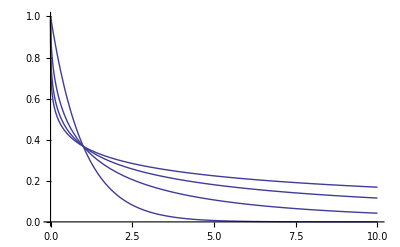

-(ⅇ^(-R^(1/n)) R^(-1+1/n))/n

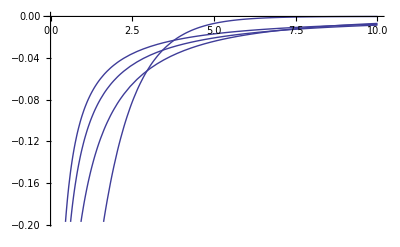

```mathematica
Plot[Table[Exp[-R^(1/n)],{n,1,4}],{R,0,10},PlotRange->{0,1}]
D[Exp[-R^(1/n)],R]
Plot[Table[%,{n,1,4}],{R,0,10},PlotRange->Automatic]
```

```mathematica
PDF[NormalDistribution[μ,√μ],x]
(Log@%)/.Log[Exp[x_]/y_]->x/Log[y]
D[%,μ]//FullSimplify
```

(ⅇ^(-(x-μ)^2/(2 μ)))/(√(2 π) √μ)

Log[(ⅇ^(-(x-μ)^2/(2 μ)))/(√(2 π) √μ)]

(x^2-μ (1+μ))/(2 μ^2)

```mathematica
Log[(ⅇ^(-(x-μ)^2/(2 μ)))/(√(2 π) √μ)]/.Log[ⅇ^x_/(√(2 π) √μ)]->x-Log[√(2 π) √μ]
```

-(x-μ)^2/(2 μ)-Log[√(2 π) √μ]

```mathematica
D[-(x-μ)^2/(2 μ),μ]
```

(x-μ)^2/(2 μ^2)+(x-μ)/μ

```mathematica
D[-Log[√(2 π) √μ],μ]
```

-1/(2 μ)

```mathematica
(x-μ)^2/(2 μ^2)+(x-μ)/μ-1/(2 μ)//FullSimplify
```

(x^2-μ (1+μ))/(2 μ^2)

```mathematica
∫_0^∞ r Exp[-(r+r0)^2/2]ⅆr
```

ⅇ^(-r0^2/2)-√(π/2) r0 Erfc[r0/(√2)]

```mathematica
D[Exp[-(√rs+r0)^2/2]/(ⅇ^(-r0^2/2)-√(π/2) r0 Erfc[r0/(√2)]),{{rs,r0}}]
%/.ⅇ^(-1/2 (r0+√rs)^2)->p (ⅇ^(-r0^2/2)-√(π/2) r0 Erfc[r0/(√2)])/.{√rs->r,1/(√rs)->1/r}
```

{-(ⅇ^(-1/2 (r0+√rs)^2) (r0+√rs))/(2 √rs (ⅇ^(-r0^2/2)-√(π/2) r0 Erfc[r0/(√2)])),(ⅇ^(-1/2 (r0+√rs)^2) √(π/2) Erfc[r0/(√2)])/((ⅇ^(-r0^2/2)-√(π/2) r0 Erfc[r0/(√2)])^2)+(ⅇ^(-1/2 (r0+√rs)^2) (-r0-√rs))/(ⅇ^(-r0^2/2)-√(π/2) r0 Erfc[r0/(√2)])}

{-(p (r+r0))/(2 r),p (-r-r0)+(p √(π/2) Erfc[r0/(√2)])/(ⅇ^(-r0^2/2)-√(π/2) r0 Erfc[r0/(√2)])}

#### Moffat profile:

```mathematica
p[rs_]=2 (β-1)(1+rs)^-β;
Integrate[r p[r^2],{r,0,∞},Assumptions->β>1]
D[p[rs],{{rs,β}}]
%//FullSimplify
```

1

{-2 (1+rs)^(-1-β) (-1+β) β,2 (1+rs)^-β-2 (1+rs)^-β (-1+β) Log[1+rs]}

{-2 (1+rs)^(-1-β) (-1+β) β,(1+rs)^-β (2-2 (-1+β) Log[1+rs])}

```mathematica
D[x^y,y]
```

x^y Log[x]